# Spike Parser

## Setup (automatically initialized when this notebook is opened)

### Function definitions

#### OrganizeWFData[fileName_,timeBounds_]

This function takes the filename of a waveform and extracts the coordinates of the waveform plot.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data should be taken.

As output, this function returns a single data member which is organized as {}.

```mathematica
OrganizeWFData[fileName_]:=Module[{axesLabel,d,i},
i=Import[fileName,"Data"];
axesLabel=i⟦1⟧;
d=i⟦2;;⟧;
Return[{axesLabel,d}];
](* OrganizeWFData Module *)
```

#### GetWFPlotData[data_,x_,y_]

This function is used to get the waveform’s plot data for any given coordinate.  As input, it takes the data structure that is setup using the OrganizeFGData method, and an (x, y) coordinate.  Note: This function is overloaded to accept either individual x and y coordinates or a list form of an {x,y} coordinate.

```mathematica
GetWFPlotData[data_,x_,y_]:=Module[{neuronIndices,validCondition,xyCoord,tempIndices},
neuronIndices=Transpose[Drop[Transpose[Position[data,{x,y}]],-1]];
xyCoord ={data⟦#⟦1⟧,1⟧,data⟦#⟦1⟧,2⟧,data⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,2⟧}&/@neuronIndices;
xyCoord=GatherBy[xyCoord,#⟦1⟧&];
Return[xyCoord];
](* Module *)
GetWFPlotData[data_,coord_]:=Module[{neuronIndices,validCondition,xyCoord,tempIndices},
neuronIndices=Transpose[Drop[Transpose[Position[data,coord]],-1]];
xyCoord ={data⟦#⟦1⟧,1⟧,data⟦#⟦1⟧,2⟧,data⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,2⟧}&/@neuronIndices;
xyCoord=GatherBy[xyCoord,#⟦1⟧&];
Return[xyCoord];
](* Module *)
```

### Ask user to select an input file with the waveform data

This section opens a system dialog box that asks the user to select a waveform file with the waveform trace.  It then sets the default working directory equal to the directory where this file is located.

```mathematica
fileName=SystemDialogInput["FileOpen","/home/noza/work/Mathematica/Scripts", WindowTitle->"Select Simulation Waveform File (*.txt)"];
workingDir=DirectoryName[fileName];
SetDirectory[workingDir];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]]
Print[Style["File Name: ", FontFamily->"Helvetica", Bold],FileNameTake[fileName]];
```

Working Directory:  /home/noza/work/Mathematica/Scripts

Sample of filenames in pwd: LPFWaveform_Im_tau_0.01.txt

## Information Processing (Run-time)

### Process Waveform data from input file

```mathematica
timeBounds ={0.5,1.5};
data=.;
AbsoluteTiming[data=OrganizeWFData[fileName]];
axesLabel=data⟦1⟧;
d=data⟦2⟧;
selectedData=Select[d,#⟦1⟧>timeBounds⟦1⟧&];
selectedData=Select[selectedData,#⟦1⟧<=timeBounds⟦2⟧&];
```

#### Plot Data

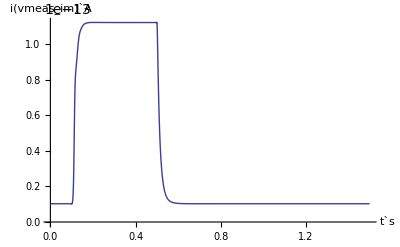

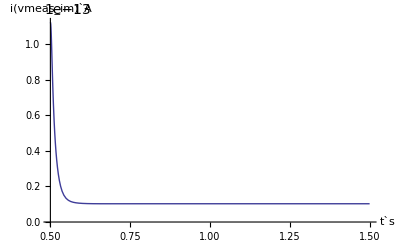

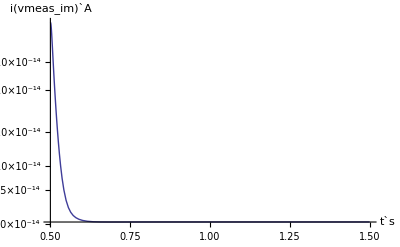

```mathematica
ListLinePlot[d,AxesLabel->axesLabel]
ListLinePlot[selectedData,AxesLabel->axesLabel]
ListLogPlot[selectedData,AxesLabel->axesLabel,Joined->True]
```

1.12179×10^-13

1.02667×10^-14

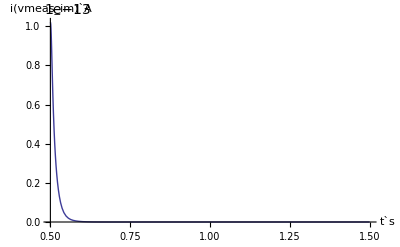

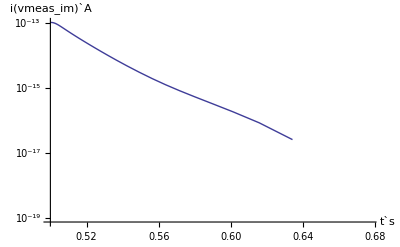

```mathematica
Isat=Max[Transpose[selectedData]⟦2⟧]
offset=Last[Transpose[selectedData]⟦2⟧]
ListLinePlot[selectedData-offset,AxesLabel->axesLabel]
ListLogPlot[selectedData-offset,AxesLabel->axesLabel,Joined->True]
```

```mathematica
FindFit[(selectedData-offset)/Isat, ⅇ^(-t/τ),{τ},t,Method->"QuasiNewton"]
```

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

```mathematica
Log[selectedData-offset]
```

(-0.693145 | -29.9154
-0.693139 | -29.9154
-0.693121 | -29.9154
-0.693065 | -29.9152
-0.692885 | -29.9148
-0.69231 | -29.9147
-0.690758 | -29.924
-0.68937 | -29.9446
-0.687953 | -29.9767
-0.686565 | -30.0171
-0.685161 | -30.0651
-0.683674 | -30.1213
-0.682029 | -30.1878
-0.680107 | -30.2685
-0.677687 | -30.3719
-0.674431 | -30.5114
-0.670064 | -30.6962
-0.666383 | -30.8497
-0.662523 | -31.0083
-0.65861 | -31.1671
-0.654378 | -31.3373
-0.649685 | -31.5243
-0.644359 | -31.7349
-0.638206 | -31.9759
-0.630993 | -32.2551
-0.622417 | -32.5819
-0.612061 | -32.9675
-0.59932 | -33.4275
-0.586149 | -33.8834
-0.573166 | -34.3085
-0.559619 | -34.7268
-0.545058 | -35.1568
-0.528587 | -35.6363
-0.509031 | -36.2202
-0.485121 | -36.998
-0.455601 | -38.1846
-0.419332 | -41.9574+3.14159 ⅈ
-0.374525 | -39.4864+3.14159 ⅈ
-0.317394 | -39.8779+3.14159 ⅈ
-0.239531 | -41.1101+3.14159 ⅈ
-0.148503 | Indeterminate
-0.0650752 | -43.7491
0.0119286 | Indeterminate
0.0834216 | Indeterminate
0.0953102 | Indeterminate
0.114043 | Indeterminate
0.171749 | Indeterminate
0.232999 | Indeterminate
0.290712 | Indeterminate
0.345276 | Indeterminate
0.397016 | Indeterminate
0.405465 | Indeterminate)

## Appendix